```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
ClearAll[f,x]
f[x_/;MatchQ[x,{{_Symbol->_InterpolatingFunction}..}]]:=Length[x]
```

```mathematica
f[s]
```

1

```mathematica
Table[i[[1]][t],{i,{cat->dog,sheep->horse}/.Rule->List}]
```

{cat[t],sheep[t]}

```mathematica
{cat->dog,sheep->horse}
```

{cat→dog,sheep→horse}

```mathematica
{cat->dog,sheep->horse}/.Rule->List
```

{{cat,dog},{sheep,horse}}

```mathematica
Abs[-8]:=8
```

SetDelayed::write: Tag Abs in Abs[-8] is Protected.

$Failed

```mathematica
Unprotect[Plot]
```

{Plot}

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

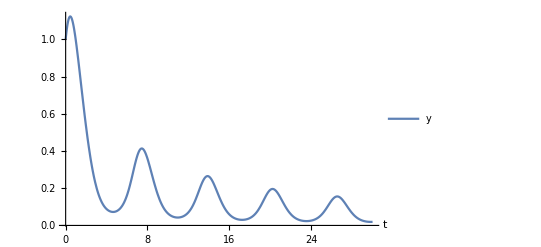

```mathematica
Plot[s]
```

```mathematica
Join[{t},(s/.Rule->List)⟦1⟧⟦1⟧⟦2⟧["Domain"]⟦1⟧]
```

{t,0.,30.}

```mathematica
(s/.Rule->List)[[1]][[1]][[2]]["Domain"][[1]]
```

{0.,30.}

```mathematica
s
```

```mathematica
Evaluate[Table[i[t],{i,simpleStocks[s]}]/.s[[1]]]
```

Table::iterb: Iterator {i,simpleStocks[{{y→InterpolatingFunction[{{«2»}},{5,7,1,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«338»}},{Developer`PackedArrayForm,{«339»},{«676»}},{Automatic}]}}]} does not have appropriate bounds.

Table::iterb: Iterator {i,simpleStocks[{{InterpolatingFunction[{{«2»}},{5,7,1,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«338»}},{Developer`PackedArrayForm,{«339»},{«676»}},{Automatic}]→InterpolatingFunction[{{«2»}},«3»,{Automatic}]}}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[i[t],{i,simpleStocks[{{InterpolatingFunction[{{0., 30.}}, <>]→InterpolatingFunction[{{0., 30.}}, <>]}}]}]

```mathematica
Evaluate[Table[(i/.Rule->List)[[1]][[1]][t],{i,s}]]
```

{y[t]}

```mathematica
Plot[Evaluate[Table[(i/.Rule->List)[[1]][[1]][t],{i,s}]]/.s,Evaluate@Join[{t},(s/.Rule->List)[[1]][[1]][[2]]["Domain"][[1]]],PlotRange->All,
AxesLabel-> Automatic,PlotLegends-> Map[ToString,Table[(i/.Rule->List)[[1]][[1]],{i,s}]]]
```

-Graphics-